# QKT

## Setup

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Get["C:\\Users\\Miguel\\Github\\Chaotic_eigenfunctions\\Resonant_k\\QKT_full.wl"];
```

```mathematica
LaunchKernels[14];
```

## Grid

```mathematica
radius=2;
delta=0.025;
xCoords=Range[-radius,radius,delta];
yCoords=Range[-radius,radius,delta];
gridPointsRaw=Flatten[Table[{x,y},{x,xCoords},{y,yCoords}],1];
(*Keep only those inside disk*)
region=Select[gridPointsRaw,Norm[#]<radius&];
region//Dimensions
```

{20069,2}

```mathematica
ListPlot[region,AspectRatio->1]
```

```mathematica
GetQKTParityEigensystem[jParam_, alphaParam_, kParam_] :=
  Module[{mat, d, idx, matEven, matOdd, esEven, esOdd,
          phEven, phOdd, vecsEven, vecsOdd, idxE, idxO,
          fullVecsEven, fullVecsOdd},
    mat = Floqsym[jParam, alphaParam, kParam];
    d = 2 jParam + 1;
    idx = ParitySectorIndices[jParam];
    matEven = mat[[idx["Even"], idx["Even"]]];
    matOdd  = mat[[idx["Odd"], idx["Odd"]]];
    esEven = Eigensystem[matEven, Method -> "Direct"];
    esOdd  = Eigensystem[matOdd, Method -> "Direct"];
    phEven = Mod[Arg[esEven[[1]]], 2 Pi];
    phOdd  = Mod[Arg[esOdd[[1]]], 2 Pi];
    idxE = Ordering[phEven]; idxO = Ordering[phOdd];
    vecsEven = esEven[[2, idxE]];
    vecsOdd  = esOdd[[2, idxO]];
    fullVecsEven = Table[
      Module[{vec = ConstantArray[0. + 0. I, d]},
        vec[[idx["Even"]]] = vecsEven[[i]]; vec],
      {i, Length[idx["Even"]]}];
    fullVecsOdd = Table[
      Module[{vec = ConstantArray[0. + 0. I, d]},
        vec[[idx["Odd"]]] = vecsOdd[[i]]; vec],
      {i, Length[idx["Odd"]]}];
    <|"Even" -> <|"Quasienergies" -> esEven[[1]],
                  "Phases" -> phEven,
                  "Vectors" -> vecsEven,
                  "FullVectors" -> fullVecsEven|>,
      "Odd"  -> <|"Quasienergies" -> esOdd[[1]], 
                  "Phases" -> phOdd,
                  "Vectors" -> vecsOdd,
                  "FullVectors" -> fullVecsOdd|>|>
  ];
```

## Method

```mathematica
(*Floquet parameters*)
J=200;
d=2 J+1;
α=Pi/Sqrt[8];
k=J*Pi(2/5.);
```

```mathematica
ops=generateSpinOperators[J];
```

```mathematica
Print["Generating coherent states over ",Length[region]," points..."];
coherentStateGenerator=generateCoherentStateCompiler[];
statesCompiled=ParallelMap[coherentStateGenerator[J,#[[1]],#[[2]]]&,region,Method->"CoarsestGrained"  (*Optional:better batching*)];
```

Generating coherent states over 20069 points...

```mathematica
Print["Computing Floquet matrix..."];
data=GetQKTParityEigensystem[J,α,k];
```

Computing Floquet matrix...

```mathematica
neweigenvec=Join[data["Even","FullVectors"],data["Odd","FullVectors"]];
```

```mathematica
Print["Projecting states into Floquet basis..."];
overlaps=Conjugate[neweigenvec].Transpose[statesCompiled];
Print["Computing IPRs..."];
iprCompiled=Total[Abs[overlaps]^4,{1}];
```

Projecting states into Floquet basis...

Computing IPRs...

```mathematica
newdata=Table[-Log[i]/Log[2 J+1],{i,iprCompiled}];
```

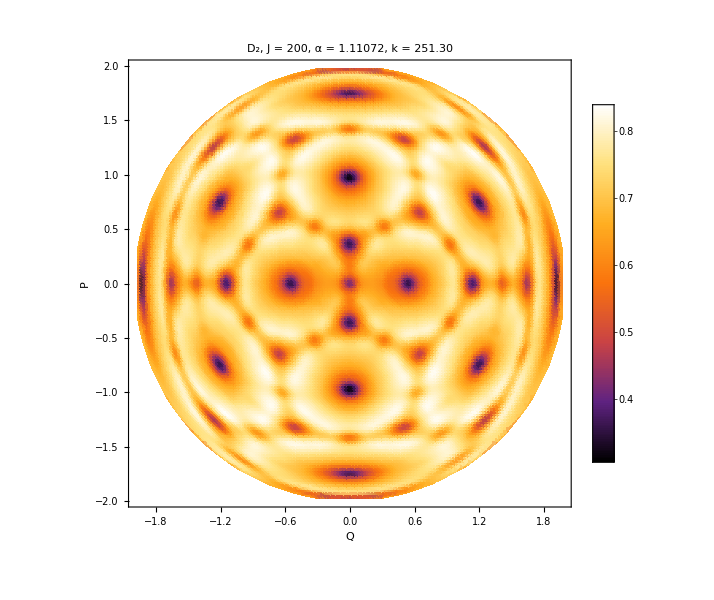

```mathematica
plot=ListDensityPlot[Transpose[{region[[All,1]],region[[All,2]],newdata}],PlotRange->All,PlotTheme->"Detailed",ColorFunction->"SunsetColors",PlotLabel->Style["D₂, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[NumberForm[k,{4,2}]],25,Black],ImageSize->600,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90 Degree]},LabelStyle->Directive[30,Black],AspectRatio->1,Frame->True,InterpolationOrder->3]
```

```mathematica
Export["husimid2.png",plot]
```

husimid2.png

```mathematica
(* ── Quasienergies (both parities, same order as neweigenvec) ── *)
quasienergies = Join[data["Even", "Phases"], data["Odd", "Phases"]];
```

```mathematica
s = 5;
targets = Table[p * Pi / s, {p, 0, 2s - 1}];

(* wrap distance accounting for 2π periodicity *)
delta = Map[
  Min[Min[Abs[# - targets]], Min[Abs[# - targets - 2Pi]], Min[Abs[# - targets + 2Pi]]] &,
  quasienergies
];
```

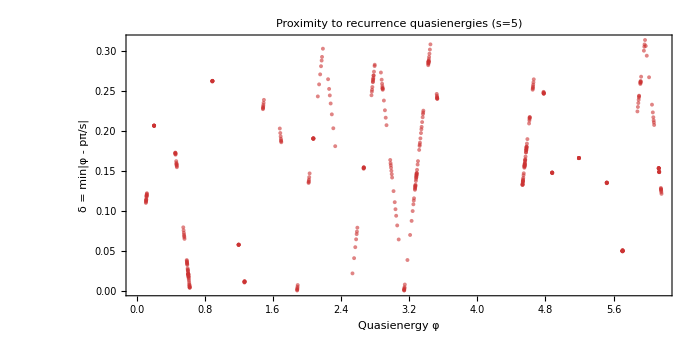

```mathematica
ListPlot[Transpose[{quasienergies,delta}],PlotStyle->Directive[PointSize[0.004],Opacity[0.6],RGBColor[0.8,0.2,0.2]],FrameLabel->{Style["Quasienergy φ",16],Style["δ = min|φ - pπ/s|",16]},PlotLabel->Style["Proximity to recurrence quasienergies  (s="<>ToString[s]<>")",14],LabelStyle->Directive[14,Black],ImageSize->700,AspectRatio->1/2,Frame->True]
```

```mathematica
thresholds={0.01,0.05,0.10,0.15};
Table[{thresh,Count[delta,d_/;d<thresh]},{thresh,thresholds}]//TableForm
```

0.01 | 21
0.05 | 64
0.1 | 93
0.15 | 177

```mathematica
(* ── Select eigenstates with delta < 0.02 (yields 60 states) ── *)
selectedIdx = Flatten[Position[delta, d_ /; d < 0.01]];

nPlot = Length[selectedIdx];  (* should be 60 *)
Print["Selected ", nPlot, " eigenstates with δ < 0.02"];

(* ── Sort selected by delta ascending within the selection ── *)
selectedIdx = selectedIdx[[Ordering[delta[[selectedIdx]]]]];
```

Selected 21 eigenstates with δ < 0.02

# Phase space s

```mathematica
(*══ Parity operator weights[M'_s]_{mm} ══════════════════════════════════ User's convention:lowest-weight reference (|J,-J⟩).The (-1)^j factor relabels m->-m relative to Koczor et al.(2020),Eq.(5).*)(*══ Numerically Stable Parity Weights ══════════════════════════════════*)generateParityWeights[Jval_,sval_]:=Module[{Rsphere,logGammaList,gammaList,mList},Rsphere=Sqrt[Jval/(2 Pi)];
(*Shift to logarithmic operations to prevent overflow for J>85*)logGammaList=Table[Log[Rsphere]+0.5 Log[4 Pi]+LogGamma[2 Jval+1]-0.5 (LogGamma[2 Jval+j+2]+LogGamma[2 Jval-j+1]),{j,0,2 Jval}];
gammaList=Exp[logGammaList];
mList=Range[-Jval,Jval];
N[Table[(1/Rsphere) Sum[(-1)^j*Sqrt[(2 j+1)/(4 Pi)]*gammaList[[j+1]]^(-sval)*Sqrt[(2 j+1)/(2 Jval+1)]*ClebschGordan[{Jval,m},{j,0},{Jval,m}],{j,0,2 Jval}],{m,mList}]]];

(*══ One-time J_y diagonalization ════════════════════════════════════════ Returns {U,eigenvalues} such that J_y=U.diag(eigenvalues).U^†.*)
diagonalizeJy[Jval_]:=Module[{dim,mvec,JplusMat,Jy,eigvals,eigvecs},dim=2 Jval+1;
mvec=Range[-Jval,Jval];
JplusMat=SparseArray[Table[{i+1,i}->Sqrt[Jval (Jval+1)-mvec[[i]] (mvec[[i]]+1)],{i,1,dim-1}],{dim,dim}];
Jy=N[(JplusMat-Transpose[JplusMat])/(2 I)];
{eigvals,eigvecs}=Eigensystem[Normal[Jy]];
{Transpose[eigvecs],eigvals}];

(*══ Phase-space coordinate conversion ═══════════════════════════════════ Stereographic (Q,P)->spherical (θ,φ) consistent with the existing coherent-state parametrization in the notebook.*)
QPtoSpherical[{Q_,P_}]:=Module[{r2,theta,phi},r2=Q^2+P^2;
theta=If[r2<4-10.^-12,2 ArcTan[Sqrt[r2/(4-r2)]],Pi];
phi=If[r2<10.^-20,0.,ArcTan[Q,P]];
{theta,phi}];

(*══ Apply R^†(θ,φ)=e^{-iθJ_y} e^{-iφJ_z} to a matrix of eigenvectors ═ States is a (2J+1)×N_eig matrix;returns the same shape.*)
applyRotationDagger[Jval_,theta_,phi_,U_,lambdas_,states_]:=Module[{mvec,phaseZ,phaseY,c1,c2,c3,c4},mvec=Range[-Jval,Jval];
phaseZ=Exp[-I phi mvec];
phaseY=Exp[-I theta lambdas];
c1=phaseZ*states;(*J_z phase,row-wise broadcast*)c2=ConjugateTranspose[U].c1;(*rotate to J_y eigenbasis*)c3=phaseY*c2;(*J_y phase,row-wise broadcast*)c4=U.c3;(*rotate back to Dicke basis*)c4];

(*══ Phase-space distribution at all region points,all s values ════════ Returns a tensor of shape Length[region]×Length[sList]×N_eig.*)
computePhaseSpaceDistribution[Jval_,region_,U_,lambdas_,statesMatrix_,sList_,parityWeightsList_]:=ParallelMap[Module[{theta,phi,psi,pm},{theta,phi}=QPtoSpherical[#];
psi=applyRotationDagger[Jval,theta,phi,U,lambdas,statesMatrix];
pm=Abs[psi]^2;
Table[Re[parityWeightsList[[ks]].pm],{ks,1,Length[sList]}]]&,region,Method->"CoarsestGrained"];
```

```mathematica
(*══ High-Performance Phase-Space Evaluator (Strictly Typed) ════════════*)
Clear[cfPhaseSpace];
cfPhaseSpace=Compile[{{QP,_Real,1},{U,_Complex,2},{Udag,_Complex,2},{lambdas,_Real,1},{mvec,_Real,1},{states,_Complex,2},{parityWeights,_Real,2}},Module[{Q,P,r2,theta,phi,phaseZ,phaseY,c1,c2,c3,psi,pm},Q=QP[[1]];P=QP[[2]];
r2=Q^2+P^2;
(*Replaced symbolic Pi with a machine Real to prevent type branching*)theta=If[r2<4.0-10.^-12,2.0*ArcTan[Sqrt[r2/(4.0-r2)]],3.141592653589793];
phi=If[r2<10.^-20,0.0,ArcTan[Q,P]];
phaseZ=Exp[(-1.0 I)*phi*mvec];
phaseY=Exp[(-1.0 I)*theta*lambdas];
c1=phaseZ*states;
c2=Udag.c1;
c3=phaseY*c2;
psi=U.c3;
pm=Abs[psi]^2;
parityWeights.pm],RuntimeAttributes->{Listable},Parallelization->True,RuntimeOptions->"Speed" (*Forces an abort instead of a silent uncompiled fallback*)];
```

```mathematica
(* ── Free parameters ── *)
nPlot = 43;
sCanonical = {-1, 0};
sArbitrary = -0.5;        (* free choice of arbitrary s *)
allS = Append[sCanonical, sArbitrary];

(* Output folders, one per s value *)
folderMap = <|
  -1          -> "PhaseSpace_s_minus1_Husimi",
   0          -> "PhaseSpace_s_zero_Wigner",
   1          -> "PhaseSpace_s_plus1_GlauberP",
   sArbitrary -> "PhaseSpace_s_" <> ToString[sArbitrary] <> "_Custom"
|>;

(* Distinct color schemes per s for visual disambiguation *)
colorMap = <|
  -1          -> "BlueGreenYellow",
   0          -> "TemperatureMap",
   1          -> "SunsetColors",
   sArbitrary -> "Rainbow"
|>;
```

```mathematica
(*── Stage 3:Phase-Space Evaluation ──*)
selectedStates=Transpose[neweigenvec[[selectedIdx]]];

Print["Forcing strict datatypes for the compiler..."];
cRegion=N[region];
cUmat=N[Umat]+0. I;          (*Force _Complex packing*)
cUmatDag=N[UmatDag]+0. I;       (*Force _Complex packing*)
cLambda=Re[N[lambdaJy]];         (*Strip parasitic 0.I to force _Real*)
cMvec=N[Range[-J,J]];         (*Force _Real*)
cStates=N[selectedStates]+0.I; (*Force _Complex packing*)
cParity=Re[N[parityWeightsList]];(*Force _Real*)

Print["Computing phase-space distributions at ",Length[region]," points × ",Length[allS]," s values × ",nPlot," eigenvectors..."];

(*C-Compiled execution threaded over'region'*)
psResult=cfPhaseSpace[cRegion,cUmat,cUmatDag,cLambda,cMvec,cStates,cParity];
```

Forcing strict datatypes for the compiler...

Computing phase-space distributions at 31397 points × 3 s values × 43 eigenvectors...

$Aborted

```mathematica
(* ── Stage 4: create output folders ── *)
Do[
  If[!DirectoryQ[folderMap[sval]], CreateDirectory[folderMap[sval]]],
  {sval, allS}];

(* ── Stage 5: plot and export in parallel ── *)
plotTasks = Flatten[
  Table[{rankN, sval}, {rankN, 1, nPlot}, {sval, allS}], 1];

DistributeDefinitions[psResult, selectedIdx, allS, folderMap, colorMap,
  J, quasienergies, region];
```

```mathematica
(*── Stage 4:create output folders ──*)Print["Creating output directories..."];
Do[If[!DirectoryQ[folderMap[sval]],CreateDirectory[folderMap[sval]]],{sval,allS}];

(*── Stage 5:plot and export in parallel ──*)
plotTasks=Flatten[Table[{rankN,sval},{rankN,1,nPlot},{sval,allS}],1];

(*Explicitly distribute all dependencies required by the parallel sub-kernels*)
DistributeDefinitions[psResult,selectedIdx,allS,folderMap,colorMap,J,quasienergies,region];

Print["Generating and exporting ",Length[plotTasks]," phase-space plots..."];

ParallelDo[Module[{rankN,eigvecIdx,sval,sIdx,psValues,listData,plot,fname,cf,prange,vmax},rankN=task[[1]];
sval=task[[2]];
eigvecIdx=selectedIdx[[rankN]];
sIdx=Position[allS,sval][[1,1]];
(*Extract phase-space values for this specific point,s-value,and state*)psValues=psResult[[All,sIdx,rankN]];
(*Optimized array joining (orders of magnitude faster than MapThread)*)listData=Join[region,Transpose[{psValues}],2];
cf=colorMap[sval];
(*Symmetric range around 0 for the bipolar Wigner function*)vmax=Max[Abs[psValues]];
prange=If[sval==0,{-vmax,vmax},All];
plot=ListDensityPlot[listData,PlotRange->prange,PlotTheme->"Detailed",ColorFunction->cf,InterpolationOrder->1,AspectRatio->1,ImageSize->800,Frame->True,FrameLabel->{Style["Q",30,Black],Rotate[Style["P",30,Black],-90 Degree]},LabelStyle->Directive[20,Black],PlotLabel->Style["rank="<>ToString[rankN]<>"  q="<>ToString[eigvecIdx]<>"  s="<>ToString[sval]<>"  J="<>ToString[J]<>"  φ="<>ToString[NumberForm[quasienergies[[eigvecIdx]],{5,3}]]<>"  S="<>ToString[NumberForm[shannonEntropy[[eigvecIdx]],{5,3}]],18,Black]];
fname=FileNameJoin[{folderMap[sval],"rank"<>IntegerString[rankN,10,3]<>"_q"<>ToString[eigvecIdx]<>"_s"<>ToString[sval]<>".png"}];
Export[fname,plot];],{task,plotTasks},Method->"CoarsestGrained"];
```

Creating output directories...

Generating and exporting 24 phase-space plots...

Part::partd: Part specification Notebook$$27$652346`shannonEntropy⟦1⟧ is longer than depth of object.

Part::partd: Part specification Notebook$$27$652346`shannonEntropy⟦15⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

# Full test

```mathematica
(*══ High-Performance Parity Weights (Vectorized& Parallelized) ════════*)generateParityWeights[Jval_,sval_]:=Module[{Rsphere,logGammaList,gammaList,mList,coeffVec},Rsphere=Sqrt[Jval/(2 Pi)];
(*Shift to logarithmic operations to prevent overflow for J>85*)logGammaList=Table[Log[Rsphere]+0.5 Log[4 Pi]+LogGamma[2 Jval+1]-0.5 (LogGamma[2 Jval+j+2]+LogGamma[2 Jval-j+1]),{j,0,2 Jval}];
gammaList=Exp[logGammaList];
(*1. Precompute the j-dependent terms into a numerical vector*)coeffVec=N[Table[(-1)^j*Sqrt[(2 j+1)/(4 Pi)]*gammaList[[j+1]]^(-sval)*Sqrt[(2 j+1)/(2 Jval+1)],{j,0,2 Jval}]];
mList=Range[-Jval,Jval];
(*2. Distribute the m-loop across all cores and use fast dot products*)(1/Rsphere)*ParallelTable[Module[{cgVec},(*Compute the Clebsch-Gordan vector for this specific m*)cgVec=N[Table[ClebschGordan[{Jval,m},{j,0},{Jval,m}],{j,0,2 Jval}]];
(*Fast vector dot product replaces the symbolic Sum*)coeffVec.cgVec],{m,mList},Method->"CoarsestGrained"]];

(*══ One-time J_y diagonalization ════════════════════════════════════════*)
diagonalizeJy[Jval_] := Module[{dim, mvec, JplusMat, Jy, eigvals, eigvecs}, 
  dim = 2 Jval + 1;
  mvec = Range[-Jval, Jval];
  JplusMat = SparseArray[
    Table[{i + 1, i} -> Sqrt[Jval (Jval + 1) - mvec[[i]] (mvec[[i]] + 1)], {i, 1, dim - 1}], 
    {dim, dim}
  ];
  Jy = N[(JplusMat - Transpose[JplusMat])/(2 I)];
  {eigvals, eigvecs} = Eigensystem[Normal[Jy]];
  {Transpose[eigvecs], eigvals}
];

(*══ High-Performance Phase-Space Evaluator (Strictly Typed) ════════════*)
Clear[cfPhaseSpace];
cfPhaseSpace = Compile[{{QP, _Real, 1}, {U, _Complex, 2}, {Udag, _Complex, 2}, 
  {lambdas, _Real, 1}, {mvec, _Real, 1}, {states, _Complex, 2}, 
  {parityWeights, _Real, 2}},
  Module[{Q, P, r2, theta, phi, phaseZ, phaseY, c1, c2, c3, psi, pm},
    Q = QP[[1]]; P = QP[[2]];
    r2 = Q^2 + P^2;
    
    (* Replaced symbolic Pi with a machine Real to prevent type branching *)
    theta = If[r2 < 4.0 - 10.^-12, 2.0 * ArcTan[Sqrt[r2/(4.0 - r2)]], 3.141592653589793];
    phi = If[r2 < 10.^-20, 0.0, ArcTan[Q, P]];
    
    phaseZ = Exp[(-1.0 I) * phi * mvec];
    phaseY = Exp[(-1.0 I) * theta * lambdas];
    
    c1 = phaseZ * states;
    c2 = Udag . c1;
    c3 = phaseY * c2;
    psi = U . c3;
    pm = Abs[psi]^2;
    
    parityWeights . pm
  ],
  RuntimeAttributes -> {Listable},
  Parallelization -> True,
  RuntimeOptions -> "Speed" (* Forces an abort instead of a silent uncompiled fallback *)
];
```

```mathematica
(* ── Free parameters ── *)
nPlot = 21;
sCanonical = {-1, 0};
sArbitrary = 0.5;        (* free choice of arbitrary s *)
allS = Append[sCanonical, sArbitrary];
allS=sCanonical;

(* Output folders, one per s value *)
folderMap = <|
  -1         -> "PhaseSpace_s_minus1_Husimi",
   0         -> "PhaseSpace_s_zero_Wigner",
   1         -> "PhaseSpace_s_plus1_GlauberP",
  sArbitrary -> "PhaseSpace_s_" <> ToString[sArbitrary] <> "_Custom"
|>;

(* Distinct color schemes per s for visual disambiguation *)
colorMap = <|
  -1         -> "BlueGreenYellow",
   0         -> "TemperatureMap",
   1         -> "SunsetColors",
  sArbitrary -> "Rainbow"
|>;
```

```mathematica
(* ── Stage 1: parity weights ── *)
Print["Computing parity operator weights for ", Length[allS], " s values..."];
parityWeightsList = Table[generateParityWeights[J, sval], {sval, allS}];
```

Computing parity operator weights for 2 s values...

```mathematica
(* ── Stage 2: J_y diagonalization ── *)
Print["Diagonalizing J_y (dimension ", 2 J + 1, ")..."];
{Umat, lambdaJy} = diagonalizeJy[J];
UmatDag = ConjugateTranspose[Umat]; (* Pre-allocate Hermitean adjoint *)
```

Diagonalizing J_y (dimension 401)...

```mathematica
(* ── Stage 3: Phase-Space Evaluation ── *)
selectedStates = Transpose[neweigenvec[[selectedIdx]]];

Print["Forcing strict datatypes for the compiler..."];
cRegion  = N[region];
cUmat    = N[Umat] + 0. I;          (* Force _Complex packing *)
cUmatDag = N[UmatDag] + 0. I;       (* Force _Complex packing *)
cLambda  = Re[N[lambdaJy]];         (* Strip parasitic 0.I to force _Real *)
cMvec    = N[Range[-J, J]];         (* Force _Real *)
cStates  = N[selectedStates] + 0.I; (* Force _Complex packing *)
cParity  = Re[N[parityWeightsList]];(* Force _Real *)
```

Forcing strict datatypes for the compiler...

```mathematica
Print["Computing phase-space distributions at ", Length[region],
  " points × ", Length[allS], " s values × ", nPlot, " eigenvectors..."];
```

Computing phase-space distributions at 20069 points × 2 s values × 21 eigenvectors...

```mathematica
(* C-Compiled execution threaded over 'region' natively *)
psResult = cfPhaseSpace[
  cRegion, cUmat, cUmatDag, cLambda, cMvec, cStates, cParity
];
```

```mathematica
(* ── Stage 4: create output folders ── *)
Print["Creating output directories..."];
Do[
  If[! DirectoryQ[folderMap[sval]], CreateDirectory[folderMap[sval]]],
  {sval, allS}
];
```

Creating output directories...

```mathematica
(* ── Stage 5: plot and export in parallel ── *)
plotTasks = Flatten[Table[{rankN, sval}, {rankN, 1, nPlot}, {sval, allS}], 1];

(* Distributed dependencies updated to remove shannonEntropy *)
DistributeDefinitions[psResult, selectedIdx, allS, folderMap, colorMap, 
  J, quasienergies, region];

Print["Generating and exporting ", Length[plotTasks], " phase-space plots..."];

ParallelDo[
  Module[{rankN, eigvecIdx, sval, sIdx, psValues, listData, plot, fname, cf, prange, vmax},
    rankN     = task[[1]];
    sval      = task[[2]];
    eigvecIdx = selectedIdx[[rankN]];
    sIdx      = Position[allS, sval][[1, 1]];
    
    (* Extract phase-space values for this specific point, s-value, and state *)
    psValues  = psResult[[All, sIdx, rankN]];
    
    (* Optimized array joining *)
    listData  = Join[region, Transpose[{psValues}], 2];
    
    cf        = colorMap[sval];
    
    (* Symmetric range around 0 for the bipolar Wigner function *)
    vmax   = Max[Abs[psValues]];
    prange = If[sval == 0, {-vmax, vmax}, All];
    
    plot = ListDensityPlot[listData,
      PlotRange          -> prange,
      PlotTheme          -> "Detailed",
      ColorFunction      -> cf,
      InterpolationOrder -> 1,
      AspectRatio        -> 1,
      ImageSize          -> 800,
      Frame              -> True,
      FrameLabel         -> {Style["Q", 30, Black], Rotate[Style["P", 30, Black], -90 Degree]},
      LabelStyle         -> Directive[20, Black],
      PlotLabel          -> Style[
        "rank=" <> ToString[rankN] <>
        "  q=" <> ToString[eigvecIdx] <>
        "  s=" <> ToString[sval] <>
        "  J=" <> ToString[J] <>
        "  φ=" <> ToString[NumberForm[quasienergies[[eigvecIdx]], {5, 3}]],
        18, Black]
    ];
    
    fname = FileNameJoin[{folderMap[sval],
      "rank" <> IntegerString[rankN, 10, 3] <>
      "_q"   <> ToString[eigvecIdx] <>
      "_s"   <> ToString[sval] <>
      ".png"}];
      
    Export[fname, plot];
  ],
  {task, plotTasks},
  Method -> "CoarsestGrained"
];
Print["Workflow complete."];
```

Generating and exporting 42 phase-space plots...

Workflow complete.

## wigner ipr

```mathematica
(*1. Generate parity weights strictly for the Wigner function (s=0)*)
Print["Computing Wigner parity weights..."];
parityWigner={generateParityWeights[J,0]};
cParityWigner=Re[N[parityWigner]];

(*2. Prepare ALL eigenstates as a column-wise matrix for the compiled evaluator*)
cAllStates=N[Transpose[neweigenvec]]+0. I;
```

Computing Wigner parity weights...

```mathematica
(*3. Compute Wigner functions for all 2J+1 states simultaneously*)
Print["Computing Wigner functions for all ",2 J+1," eigenstates..."];
psWignerResult=cfPhaseSpace[cRegion,cUmat,cUmatDag,cLambda,cMvec,cAllStates,cParityWigner];
```

Computing Wigner functions for all 401 eigenstates...

Computing sum of squared Wigner functions...

Plotting Wigner IPR...

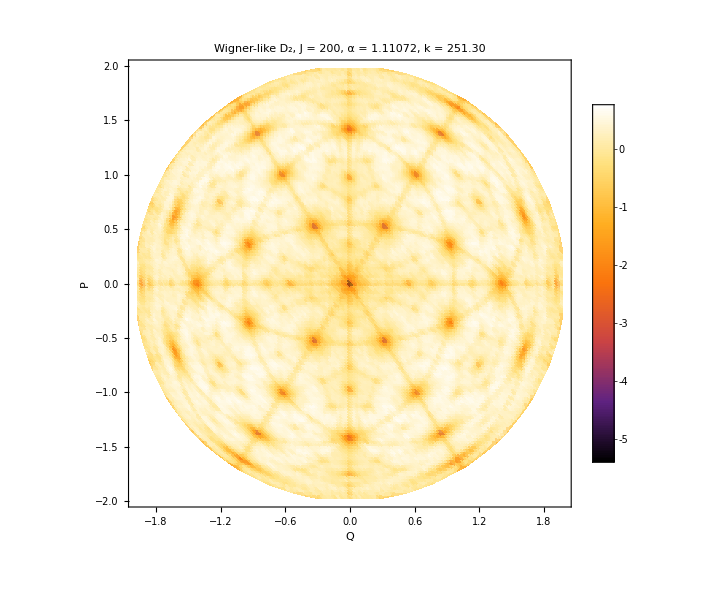

```mathematica
(*psWignerResult has dimensions:{Length[region],1 (for s=0),2J+1}*)
(*Extract the values,square them,and sum across the eigenstate dimension*)
Print["Computing sum of squared Wigner functions..."];
wignerAll=psWignerResult[[All,1,All]];
wignerSumSq=Total[wignerAll^2,{2}];

(*4. Compute the localization measure (analogous to your Husimi IPR)*)
(*Note:Vectorized Log operation is significantly faster than Table*)
newdataWigner=-Log[wignerSumSq];

(*5. Plotting using the optimized Join method*)
Print["Plotting Wigner IPR..."];
plotWigner=ListDensityPlot[Join[region,Transpose[{newdataWigner}],2],PlotRange->All,PlotTheme->"Detailed",ColorFunction->"SunsetColors",PlotLabel->Style["Wigner-like D₂, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[NumberForm[k,{4,2}]],25,Black],ImageSize->600,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90 Degree]},LabelStyle->Directive[30,Black],AspectRatio->1,Frame->True,InterpolationOrder->3]
```

```mathematica
Export["wignerd2.png",plotWigner]
```

wignerd2.png